```mathematica
Subscript[X, 0][Δ_,δ_,Ω_,γ_ ]=Min[Abs[x]/.Solve[0==2*γ*x^3-δ*Δ*x+δ*Ω/2, x, Reals]]
```

ConditionalExpression[Min[Abs[Root[δ Ω-2 δ Δ #1+4 γ #1^3&,1]],Abs[Root[δ Ω-2 δ Δ #1+4 γ #1^3&,2]],Abs[Root[δ Ω-2 δ Δ #1+4 γ #1^3&,3]]], ]

```mathematica
Subscript[b, 0][Δ_,δ_,Ω_,γ_ ] = Δ/(2*γ)-Ω/(4*Subscript[X, 0][Δ,δ,Ω,γ]*γ)
```

ConditionalExpression[Δ/(2 γ)-Ω/(4 γ Min[Abs[Root[δ Ω-2 δ Δ #1+4 γ #1^3&,1]],Abs[Root[δ Ω-2 δ Δ #1+4 γ #1^3&,2]],Abs[Root[δ Ω-2 δ Δ #1+4 γ #1^3&,3]]]), ]

```mathematica
(*All of the frequencys here are assumed to be in THz.*)
```

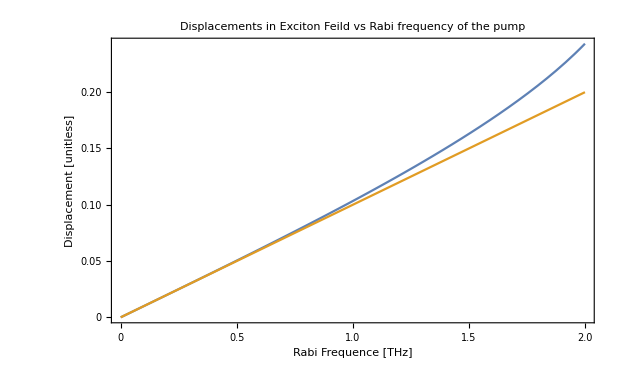

```mathematica
XPlot = Plot[{Subscript[X, 0][5,0.02, Ω, 0.15], Ω/(2*5)},{Ω,0,2}, PlotLabel->"Displacements in Exciton Feild vs Rabi frequency of the pump", 
Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"Displacement [unitless]",None},{"Rabi Frequence [THz]", None}},FrameTicks->All]
```

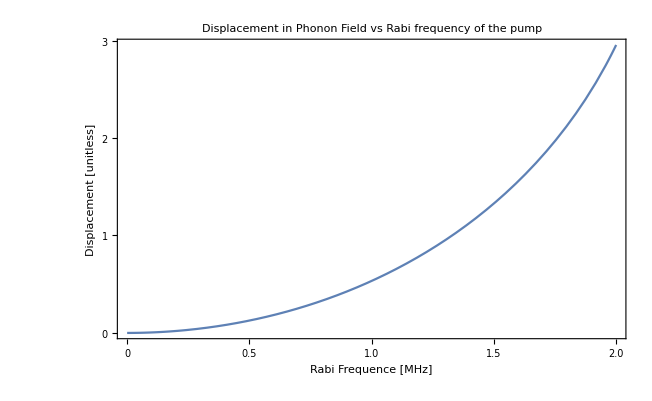

```mathematica
BPlot = Plot[Subscript[b, 0][5,0.02, Ω, 0.15],{Ω,0,2}, PlotLabel->"Displacement in Phonon Field vs Rabi frequency of the pump", 
Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"Displacement [unitless]",None},{"Rabi Frequence [MHz]", None}},FrameTicks->All]
```

```mathematica
Export["~/Desktop/XDisplacement.png",XPlot]
```

~/Desktop/XDisplacement.png

```mathematica
Export["~/Desktop/BDisplacement.png",BPlot]
```

~/Desktop/BDisplacement.png

```mathematica
Eigenvalues[{{2a,b,0},{b,a,b},{0,b,0}}]
```

{a,a-√(a^2+2 b^2),a+√(a^2+2 b^2)}